```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190226_fixed_TL_cy3_accum_15h/TL*.tif"];
```

```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_NT_*/NT*.tif" ];
```

```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_TL_*/TL*.tif" ];
```

```mathematica
myFileNames =FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed*/20190301_TA_*/TA*.tif" ];
```

```mathematica
myFileNames = FileNames["/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/20190226_fixed_TL_cy3_accum_15h/TL*"];
```

```mathematica
myFiles = Import/@myFileNames;
```

```mathematica
ImageAdjust/@myFiles[[1]]
```

{-Graphics-,-Graphics-}

```mathematica
mymeanlist = Mean/@myFiles[[2;;All,1]];
```

```mathematica
Length@myFiles-1
```

131

```mathematica
meanImgs= Sort[Table[Thread[{ mymeanlist[[i]],myFiles[[2;;All,1]][[i]] }] , {i,1,Length@myFiles-1}] ] ;
```

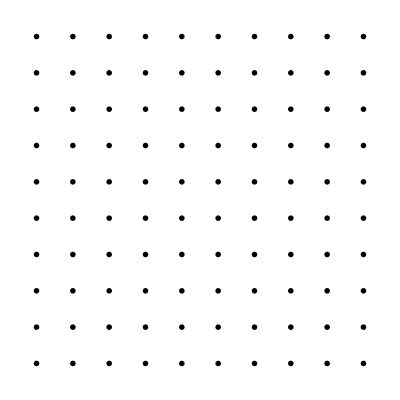

```mathematica
meanImgs100Sorted = RandomSample[meanImgs,100]//Sort//#[[All,2]]&;
myCellsGsorted = Table[ImageResize[ImageAdjust[meanImgs100Sorted[[img]],{0,0,1},{.0001,.2}],{64,64}],{img,1,100,1}];
myGrid = GraphicsGrid[Partition[myCellsGsorted,10]]
```

```mathematica
Colorize[-Graphics-,ColorFunction->"AvocadoColors",ColorFunctionScaling->False ]//ImageResize[#,{4*64,4*64}]&
```

```mathematica
myCellsGsortedAvocado0 = Table[ImageResize[ImageAdjust[meanImgs100Sorted[[img]],{0,0,1},{.01,.15}],{64,64}],{img,1,100,1}];
myCellsGsortedAvocado = Colorize[#,ColorFunction->"AvocadoColors",ColorFunctionScaling->False ]&/@myCellsGsortedAvocado0;
myGrid = GraphicsGrid[Partition[myCellsGsortedAvocado,10]]
```

-Graphics-

```mathematica
(*Looks a little blown out when you use:    {1,2,1},{.0001,.2} 
*)
```

```mathematica
(*USE THIS ONLY FOR NT!!! To get rid of that repeat cell asshole 
*)

(*gap = 77;
pseudoSortNTONLY0= meanImgs//Sort//#[[All,2]]&;
pseudoSortNTONLY00 = Join[pseudoSortNTONLY0[[1;;gap-1]],pseudoSortNTONLY0[[gap+1;;All]]  ];
pseudoSortNTONLY = Table[ImageResize[ImageAdjust[pseudoSortNTONLY00[[img]],{0,0,1},{.0001,.2}],{64,64}],{img,1,100,1}];
GraphicsGrid[Partition[pseudoSortNTONLY,10]]
```

```mathematica
(*
myCellsGsortedAvocado = Colorize[#,ColorFunction->"AvocadoColors",ColorFunctionScaling->False ]&/@pseudoSortNTONLY;
myGrid = GraphicsGrid[Partition[myCellsGsortedAvocado,10]]
```

```mathematica
myCellsG = Table[ImageResize[ImageAdjust[myFiles[[img,1]],{1,2,1},{.0001,.2}],{64,64}],{img,2,101,1}];
GraphicsGrid[Partition[myCellsG,10]]
```

```mathematica
myCellsG = Table[ImageResize[ImageAdjust@myFiles[[img,1]],{64,64}],{img,1,101,1}];
gridG=GraphicsGrid[Partition[myCellsG,10]]
```

```mathematica
myCellsB = Table[ImageResize[
ImageAdjust[myFiles[[img,2]],{1,1,1},{.00001,.075}],{64,64}],{img,1,100,1}];
gridB=GraphicsGrid[Partition[myCellsB,10]]
```

```mathematica
dummyImg = Flatten[Table[Flatten@Table[0,1,64],1,64],1]//Image
dummyImgW = Flatten[Table[Flatten@Table[1,1,64],1,64],1]//Image
dummyImg//ImageDimensions
```

-Graphics-

-Graphics-

{64,64}

```mathematica
dummyImgs =GraphicsGrid[  Partition[Table[-Graphics-,100],10]  ];
```

```mathematica
ColorNegate[(myCellsG[[1]]+ myCellsB[[1]])/.5]
```

-Graphics-

```mathematica
GraphicsGrid[Partition[ Table[ColorCombine[{myCellsB[[i]], myCellsG[[i]], dummyImg,ColorNegate[(myCellsG[[i]]+ myCellsB[[i]])/1.25]},"CMYK"],  {i,1,100}],10]]
```

-Graphics-

```mathematica
myTable = ColorCombine[{dummyImgs,gridG,gridB}]
```

-Graphics-

```mathematica
myFileNames[[1]]
```

/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/20190301_TL_fix_transf_cy3-flag-fab_accum/TL00.tif

```mathematica
(*Export[ "/Volumes/BITTY/_long_timeframe_transient_mini/Fixed Cell/_fixed_cy3-FLAG-Fab_15h_accum/G_TL1_grid.tif"  ,tl1accumgrid]
```